```mathematica
data=Import["../fatal-police-shootings-data.csv"];
```

```mathematica
allDates=data[[2;;, 3]];
dates=Select[allDates,StringStartsQ[#,{"2018"}]&];
counts:=Counts[dates];
days:=365;
```

```mathematica
categories=KeySort[Append[Counts[Values[counts]], 0->days-Length[counts]]];
n=Max[Keys[categories]];
For[i=1,i<n,i++,If[KeyExistsQ[categories,i],None,categories[i]=0]];
{n,categories}
```

{10,<|0→35,1→71,2→76,3→68,4→59,5→28,6→13,7→8,8→3,9→3,10→1|>}

```mathematica
k=Sum[x*categories[x],{x,Keys[categories]}]/days;
{k,N[k]}
```

{998/365,2.73425}

```mathematica
a=Map[Function[x, (ⅇ^-k k^x)/(x!)],Range[0,n-1]];
a=Append[a,1-Accumulate[a][[-1]]];
{N[a],days*N[a]}
a[[-3]]+=a[[-2]]+a[[-1]];
a=Delete[Delete[a,-1],-1];
expect=days*a;
n=Length[expect];
{N[a],N[expect]}
```

{{0.0649429,0.17757,0.24276,0.221255,0.151242,0.0827064,0.0376899,0.0147219,0.00503168,0.00152865,0.000551702},{23.7042,64.813,88.6074,80.7582,55.2032,30.1878,13.7568,5.37351,1.83656,0.557957,0.201371}}

{{0.0649429,0.17757,0.24276,0.221255,0.151242,0.0827064,0.0376899,0.0147219,0.00711203},{23.7042,64.813,88.6074,80.7582,55.2032,30.1878,13.7568,5.37351,2.59589}}

```mathematica
observe=Values[categories];
observe[[-3]]+=observe[[-2]]+observe[[-1]];
observe=Delete[Delete[observe,-1],-1]
```

{35,71,76,68,59,28,13,8,7}

```mathematica
X2=∑_(i=1)^n (expect[[i]]-observe[[i]])^2/expect[[i]];
N[X2]
```

18.9998

```mathematica
P=1-CDF[ChiSquareDistribution[n],X2];
N[P]
```

0.0251944

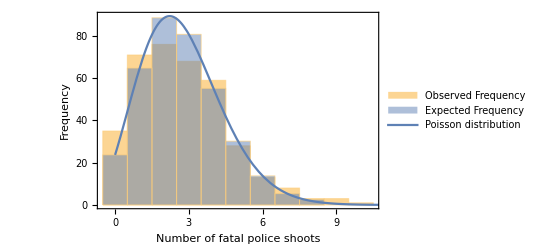

```mathematica
n=Length[observe];
weightedObserveData=WeightedData[Keys[categories],Values[categories]];
weightedExpectData=WeightedData[Range[0,n-1],expect];
fig=Show[
Histogram[
{Legended[weightedObserveData,"Observed Frequency"],
Legended[weightedExpectData,"Expected Frequency"]},n,
Frame->{True,True,False,False},
FrameTicks->{Range[0,n+1],Automatic},
FrameLabel->{"Number of fatal police shoots","Frequency"}
],
Plot[
Legended[Evaluate[days*PDF[PoissonDistribution[k],x]],"Poisson distribution"],{x,0,n+2},
PlotStyle->Thick,
PlotLegends->Automatic
]]
Export["q3-2018-exp.eps",fig];
```